```mathematica
Quit[]
```

# Calculations

```mathematica
<<FeynCalc`
<<MyPackages`HistV2`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

## Calculations

### Initial constants

```mathematica
Y=1/2;
Gf=1.166*10^(-5);
dm232=1;
a1=1.07;
Fm2320=1/(3*π);
mπ=0.13957;
fπ=0.1304;
mρ=0.7665;
fρ=0.216;
ma1=1.230;
fa1=0.238;
SetAttributes[V,Orderless];
V["c","b"]=0.0411;V["c","s"]=0.974;V["c","d"]=0.225;
V["u","b"]=0.00357;V["u","s"]=0.225;V["u","d"]=0.974;
```

### Spectral functions constants

```mathematica
SetDirectory[NotebookDirectory[]];
Fq2π=HST2D[ReadList["plot2pi.txt",{Number,Number}], ShowErrors-> False];
Fq3π=HST2D[ReadList["plot3pi.txt",{Number,Number}], ShowErrors-> False];
Fq4πa1=HST2D[ReadList["plot4pi.txt",{Number,Number}], ShowErrors-> False];
Fq4πb1 = HST2D[ReadList["omega.txt", {Number, Number}], ShowErrors-> False];
Fq5π=HST2D[ReadList["plot5pi.txt",{Number,Number}], ShowErrors-> False];
```

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ScalarProduct[p1,p1]=m1^2;
ScalarProduct[p2,p2]=m2^2;
ScalarProduct[p1,p2]=(m1^2+m2^2-q2)/2;
q=p1-p2;
H =SpinorUBar[p2,m2].GA[μ].(1+GA[5]).SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
H2=H*cH;
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[q,μ]*FV[q,α]-q2*MT[μ,α])]];
λ:=√(1-((m2+√q2)/m1)^2)*√(1-((m2-√q2)/m1)^2);
HT:=λ*H4;
m1=1.776;
m2=0;
h=6.5*10^-25;τ=290*10^-15;
Γτ=h/τ;
```

```mathematica
(*Decay to 2π*)
Clear[Br, BrNorm];
BrNorm=0.2549;
dΓ2π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq2π[q2];
Γ2π=NIntegrate[dΓ2π, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π/Γτ;
Const2π=BrNorm/Br
Γ2π=Const2π*NIntegrate[dΓ2π, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π/Γτ;
Error=Br/BrNorm
```

0.35257

1.

```mathematica
(*Decay to 3π*)
Clear[Br, BrNorm];
BrNorm=0.0903;
dΓ3π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq3π[q2];
Γ3π=NIntegrate[dΓ3π, {q2,9mπ^2,(m1-m2)^2}];
Br=Γ3π/Γτ;
Const3π=BrNorm/Br
Γ3π=Const3π*NIntegrate[dΓ3π, {q2,9mπ^2,(m1-m2)^2}];
Br=Γ3π/Γτ;
Error=Br/BrNorm
```

7.0067

1.

```mathematica
(*Decay to 4π a1*)
Clear[Br, BrNorm];
BrNorm=0.0274;
dΓ4πa1= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq4πa1[q2];
Γ4πa1=NIntegrate[dΓ4πa1, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4πa1/Γτ;
Const4πa1=BrNorm/Br
Γ4πa1=Const4πa1*NIntegrate[dΓ4πa1, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4πa1/Γτ;
Error=Br/BrNorm
```

6435.91

1.

```mathematica
(*Decay to 4π b1*)
Clear[Br, BrNorm];
BrNorm=0.0188;
dΓ4πb1= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq4πb1[q2];
Γ4πb1=NIntegrate[dΓ4πb1, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4πb1/Γτ;
Const4πb1=BrNorm/Br
Γ4πb1=Const4πb1*NIntegrate[dΓ4πb1, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4πb1/Γτ;
Error=Br/BrNorm
```

27847.6

1.

```mathematica
(*Decay to 5π*)
Clear[Br, BrNorm];
BrNorm=0.000769;
dΓ5π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq5π[q2];
Γ5π=NIntegrate[dΓ5π, {q2,25mπ^2,(m1-m2)^2}];
Br=Γ5π/Γτ;
Const5π=BrNorm/Br
Γ5π=Const5π*NIntegrate[dΓ5π, {q2,25mπ^2,(m1-m2)^2}];
Br=Γ5π/Γτ;
Error=Br/BrNorm
```

32921.3

1.

```mathematica
Fq2π=Const2π*Fq2π;
Fq3π=Const3π*Fq3π;
Fq4πa1=Const4πa1*Fq4πa1;
Fq4πb1=Const4πb1*Fq4πb1;
Fq5π=Const5π*Fq5π;
Fq4πfull = Fq4πa1+Fq4πb1;
```

InterpolatingFunction::dmval: Input value TraditionalForm`{0.316318} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value TraditionalForm`{0.320994} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value TraditionalForm`{0.325704} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
(* Select every 10th point from Fq5π *)
$Fq5π = HST2D[Table[Fq5π⟦1,i⟧,{i,1,Length[Fq5π⟦1⟧],10}]];
$$Fq5π = HST2D[Table[{q2, Fq5π[q2]},{q2,25mπ^2, 4.67^2,(4.67^2-25mπ^2)/200}]];
```

InterpolatingFunction::dmval: Input value TraditionalForm`{0.486995} lies outside the range of data in the interpolating function. Extrapolation will be used.

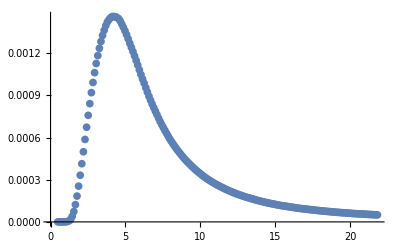

```mathematica
PlotHST[$$Fq5π]
```

```mathematica
(* Select every 10th point from Fq3π *)
$Fq3π = HST2D[Table[Fq3π⟦1,i⟧,{i,1,Length[Fq3π⟦1⟧],10}]];
$$Fq3π = HST2D[Table[{q2, Fq3π[q2]},{q2,9mπ^2, 4.67^2,(4.67^2-25mπ^2)/100}]];
```

InterpolatingFunction::dmval: Input value TraditionalForm`{0.175318} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
Fq5π[[1,1]]
```

{0.544454,7.68664×10^-13}

### Clear

```mathematica
Clear[Γ2π,Γ3π,Γ4πa1,Γ4πb1,Γ5π,dΓ2π,dΓ3π,dΓ4πa1,dΓ4πb1,dΓ5π,$dΓ5π,H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ClearScalarProducts;
```

### Init

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,m232,q,m1,m2,m3,m4,Br,f1,f2,g1,g2];
ScalarProduct[p11,p11]=m1^2;
ScalarProduct[p22,p22]=m2^2;
ScalarProduct[p11,p22]=(m1^2+m2^2-m232)/2;
SetMandelstam[m232,m132,m122,p1,-p2,-pe,-ke,m1,m2,0,0];
qq=p11-p22;
q=p1-p2;
sigma=I*(GA[μ].GA[ν]-GA[ν].GA[μ])/2;
H =SpinorUBar[p22,m2].(GA[μ]*f1+I*sigma*FV[qq,ν]*f2/m1).SpinorU[p11, m1]-SpinorUBar[p22,m2].(GA[μ]*g1+ⅈ*sigma*FV[qq,ν]*g2/m1).GA[5].SpinorU[p11, m1];
HH=SpinorUBar[p2,m2].(GA[μ]*f1+I*sigma*FV[q,ν]*f2/m1).SpinorU[p1, m1]-SpinorUBar[p2,m2].(GA[μ]*g1+ⅈ*sigma*FV[q,ν]*g2/m1).GA[5].SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
cHH= ComplexConjugate[HH]/.{μ->α,ν->β};
H2=H*cH;
HH2=HH*cHH;
HH3=DiracSimplify[FermionSpinSum[HH2]]/.{DiracTrace->TR};
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α]-m232*MT[μ,α])]];
λ:=√(1-((m2+√m232)/m1)^2)*√(1-((m2-√m232)/m1)^2);
HT:=λ*H4;
(*T=Transversal*)
HL:=λ*Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α])]];
(*L=Longitudinal*)
L=SpinorUBar[pe].GA[μ].(1+GA[5]).SpinorV[ke];
cL=ComplexConjugate[L]/.{μ->α};
L2=FermionSpinSum[L*cL]/.{DiracTrace->TR};
M2=Simplify[1/2*Gf^2*Calc[HH3*L2]];
M3=M2//.m132->m1^2+m2^2-m122-m232;
E2ZV= (m122-m2^2 +m3^2)/(2*Sqrt[m122]) (*  E2^*  *);
E3ZV= (m1^2-m122-m4^2)/(2*Sqrt[m122])  (*  E3^*  *);
m23min=(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]+Sqrt[E3ZV^2-m4^2])^2;
m23max=Simplify[Calc[(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]-Sqrt[E3ZV^2-m4^2])^2]];
m12min=m2^2;
m12max=m1^2;
```

```mathematica
dΓl:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*dm232 /(2*π)*(1/(8*π))*Vckm^2*HT*Fm2320
dΓl1:=(1/2)*(1/(2*π)^3)*(1/(32*m1^3))*Vckm^2*M3;
dΓ2π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq2π[m232];
dΓ3π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq3π[m232];
dΓ4πfull:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq4πfull[m232];
dΓ4πa1:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq4πa1[m232];
dΓ4πb1:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq4πb1[m232];
dΓ5π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq5π[m232];
$dΓ5π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*$Fq5π[m232];
$$dΓ5π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*$$Fq5π[m232];
$dΓ3π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*$Fq3π[m232];
$$dΓ3π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*$$Fq3π[m232];
```

### File

```mathematica
SetDirectory[NotebookDirectory[]];
<<"wang_data.m";
decays={#["in"],#["out"]}&/@Normal[DeleteDuplicates[dsFF[All,{"in","out"}]]];
Clear[$FF];
$FF[data_]:=Module[{},Switch[data["func"],"FF",Return[data["F0"]/(1-m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];,"GG",Return[data["F0"]/(1+m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];];];
(*Clear[cS,cA];*)
Clear[FF];
FF[query_]:=Module[{$res},$res=dsFF[query];
Return[cS $FF[$res[1]]+cA $FF[$res[2]]]];
```

#### Main calculation

```mathematica
result={};
AppendTo[result,{"in","out","l nul","pi" ,"rho","2pi", "3pi", "a1->4pi","a1+b1->4pi", "5pi"}];
i=.0;
PrintTemporary[Dynamic[dec],"Завершено",Dynamic[Floor[i/36*100,-0.1]], "%" ];
Do[
{in,out}=dec;
i=i+1;
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Hρ=HT/.{m232-> mρ^2};
Γρ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fρ^2*(1/(8*π))*Vckm^2*Hρ;
Hπ=HL/.{m232-> mπ^2};
Γπ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fπ^2*(1/(8*π))*Vckm^2*Hπ;
Ha1=HT/.{m232-> ma1^2};
Γρ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\rho"]&]][[1]]["width"];
Γπ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\pi"]&]][[1]]["width"];
Γ2π=NIntegrate[dΓ2π, {m232,4mπ^2,(m1-m2)^2}];
Γ3π=NIntegrate[dΓ3π, {m232,9mπ^2,(m1-m2)^2}];
Γ4πa1=NIntegrate[dΓ4πa1, {m232,16mπ^2,(m1-m2)^2}];
Γ4πfull=NIntegrate[dΓ4πfull, {m232,16mπ^2,(m1-m2)^2}];
Γ5π=NIntegrate[dΓ5π, {m232,25mπ^2,(m1-m2)^2}];
AppendTo[result,{in,out,Floor[Chop[Γl1/fullΓ],-0.000001]*100,Floor[Chop[Γπ/fullΓ],-0.0000000001]*100,Floor[Chop[Γρ/fullΓ],-0.00000001]*100,Floor[Chop[Γ2π/fullΓ],-0.0000001]*100,Floor[Chop[Γ3π/fullΓ],-0.0000001]*100,Floor[Chop[Γ4πa1/fullΓ],-0.0000001]*100,Floor[Chop[Γ4πfull/fullΓ],-0.0000001]*100,Floor[Chop[Γ5π/fullΓ],-0.0000001]*100}];
,{dec,decays}];
result
```

$Aborted

(in | out | l nul | pi | rho | 2pi | 3pi | a1->4pi | a1+b1->4pi | 5pi)

## Make tex tables

```mathematica
dec1=Select[result,!StringFreeQ[#[[1]],"{cc}"]&];
dec2=Select[result,!StringFreeQ[#[[1]],"{bc}"]&];
dec3=Select[result,!StringFreeQ[#[[1]],"{bb}"]&];
```

```mathematica
toString[a_]:=If[Abs[a]<10^-3,ToString[ScientificForm[a,3],TeXForm],ToString[NumberForm[a,3]]];
makestr[dec_]:=Module[{str,qwert,in,out,Brlnul,Brπ,Brρ,Br2π,Br3π,Br4πa1,Br4πfull,Br5π},str="\\begin{tabular}{|l|c|c|c|c|c|c|}\n";
str=str<>"\\hline \n";
str=str<>"\\multirow{2}{*}{$\\B_1\\to\ \\B_2$}& \\multicolumn{6}{c|}{Modes}"<>"\\\\"<>"\n";
str=str<>"\\cline{2-7}"<>"\n";
str=str<>"& $l\\nu_l$ & $\\pi$ & $\\rho$ & $2\\pi$ & $3\\pi$ &   $5\\pi$"<>"\\\\"<>"\n";
str=str<>"\\hline \n";
str=str<>"\\hline \n";
Do[{in,out,Brlnul,Brπ,Brρ,Br2π,Br3π,Br4πa1,Br4πfull,Br5π}=qwert;
str=str<>"$"<>in<>"\\to\ "<>out<>"$&$"<>toString[Brlnul]<>"$&$"<>toString[Brπ]<>"$&$"<>toString[Brρ]<>"$&$"<>toString[Br2π]<>"$&$"<>toString[Br3π]<>"$&$"<> toString[Br4πa1] <>"$&$"<>toString[Br4πfull]<> "$&$" <>toString[Br5π]<>"$\\\\"<>"\n";
str=str<>"\\hline \n";,{qwert,dec}];
str=str<>"\\end{tabular}\n";
Return[str];]
```

```mathematica
str1=makestr[dec1];
str2=makestr[dec2];
str3=makestr[dec3];
```

```mathematica
DeleteFile["table11.tex"];
DeleteFile["table22.tex"];
DeleteFile["table33.tex"];
WriteString["table11.tex",str1];
WriteString["table22.tex",str2];
WriteString["table33.tex",str3];
Close["table11.tex"];
Close["table22.tex"];
Close["table33.tex"];
```

DeleteFile::fdnfnd: Directory or file table11.tex not found.

DeleteFile::fdnfnd: Directory or file table22.tex not found.

DeleteFile::fdnfnd: Directory or file table33.tex not found.

```mathematica
str1
```

\begin{tabular}{|l|c|c|c|c|c|c|}
\hline 
\multirow{2}{*}{$\B_1\to \B_2$}& \multicolumn{6}{c|}{Modes}\\
\cline{2-7}
& $l\nu_l$ & $\pi$ & $\rho$ & $2\pi$ & $3\pi$ &   $5\pi$\\
\hline 
\hline 
$\Xi_{cc}^{++}\to \Lambda_{c}^{+}$&$0.494$&$0.377$&$0.993$&$0.863$&$0.208$&$0.0302$&$0.0637$&$2.2\times 10^{-4}$\\
\hline 
$\Xi_{cc}^{++}\to \Sigma_{c}^{+}$&$0.45$&$0.244$&$1.05$&$0.9$&$0.154$&$0.0101$&$0.0189$&$4.\times 10^{-5}$\\
\hline 
$\Xi_{cc}^{++}\to \Xi_{c}^{+}$&$4.99$&$6.42$&$12.3$&$10.$&$0.634$&$0.0253$&$0.046$&$6.\times 10^{-5}$\\
\hline 
$\Xi_{cc}^{++}\to \Xi_{c}^{\prime+}$&$5.98$&$4.66$&$17.6$&$14.1$&$0.725$&$0.0172$&$0.0307$&$3.\times 10^{-5}$\\
\hline 
$\Xi_{cc}^{+}\to \Sigma_{c}^{0}$&$0.299$&$0.162$&$0.698$&$0.598$&$0.101$&$0.00659$&$0.0124$&$3.\times 10^{-5}$\\
\hline 
$\Xi_{cc}^{+}\to \Xi_{c}^{0}$&$1.65$&$2.13$&$4.08$&$3.33$&$0.21$&$0.00837$&$0.0152$&$2.\times 10^{-5}$\\
\hline 
$\Xi_{cc}^{+}\to \Xi_{c}^{\prime0}$&$1.98$&$1.55$&$5.86$&$4.68$&$0.238$&$0.0056$&$0.00999$&$1.\times 10^{-5}$\\
\hline 
$\Omega_{cc}^{+}\to \Xi_{c}^{0}$&$0.208$&$0.238$&$0.512$&$0.421$&$0.0342$&$0.00166$&$0.00306$&$1.\times 10^{-5}$\\
\hline 
$\Omega_{cc}^{+}\to \Xi_{c}^{\prime0}$&$0.249$&$0.172$&$0.711$&$0.577$&$0.039$&$0.0011$&$0.00199$&$1.\times 10^{-5}$\\
\hline 
$\Omega_{cc}^{+}\to \Omega_{c}^{0}$&$6.66$&$6.5$&$22.6$&$16.9$&$0.265$&$0.00357$&$0.00479$&$1.\times 10^{-5}$\\
\hline 
\end{tabular}

```mathematica
str2
```

\begin{tabular}{|l|c|c|c|c|c|c|}
\hline 
\multirow{2}{*}{$\B_1\to \B_2$}& \multicolumn{6}{c|}{Modes}\\
\cline{2-7}
& $l\nu_l$ & $\pi$ & $\rho$ & $2\pi$ & $3\pi$ &   $5\pi$\\
\hline 
\hline 
$\Xi_{bc}^{+}\to \Lambda_{b}^{0}$&$0.223$&$0.184$&$0.486$&$0.415$&$0.0781$&$0.00879$&$0.0187$&$5.\times 10^{-5}$\\
\hline 
$\Xi_{bc}^{+}\to \Sigma_{b}^{0}$&$0.148$&$0.0975$&$0.403$&$0.332$&$0.0292$&$0.00103$&$0.00188$&$1.\times 10^{-5}$\\
\hline 
$\Xi_{bc}^{+}\to \Xi_{b}^{0}$&$2.3$&$3.$&$5.84$&$4.72$&$0.248$&$0.00837$&$0.0151$&$2.\times 10^{-5}$\\
\hline 
$\Xi_{bc}^{0}\to \Sigma_{b}^{-}$&$0.112$&$0.0741$&$0.306$&$0.251$&$0.0217$&$7.5\times 10^{-4}$&$0.00137$&$1.\times 10^{-5}$\\
\hline 
$\Xi_{bc}^{0}\to \Xi_{b}^{-}$&$0.868$&$1.14$&$2.21$&$1.78$&$0.0922$&$0.00306$&$0.00552$&$1.\times 10^{-5}$\\
\hline 
$\Omega_{bc}^{0}\to \Xi_{b}^{-}$&$0.254$&$0.184$&$0.511$&$0.443$&$0.105$&$0.0148$&$0.0313$&$1.1\times 10^{-4}$\\
\hline 
$\Omega_{bc}^{0}\to \Omega_{b}^{-}$&$6.03$&$4.22$&$16.6$&$13.6$&$1.07$&$0.0344$&$0.0628$&$7.\times 10^{-5}$\\
\hline 
$\Xi_{bc}^{+}\to \Sigma_{c}^{++}$&$0.0035$&$7.51\times 10^{-5}$&$2.37\times 10^{-4}$&$2.4\times 10^{-4}$&$2.1\times 10^{-4}$&$2.7\times 10^{-4}$&$3.3\times 10^{-4}$&$0.0016$\\
\hline 
$\Xi_{bc}^{+}\to \Xi_{cc}^{++}$&$1.58$&$0.155$&$0.438$&$0.414$&$0.289$&$0.268$&$0.341$&$0.0703$\\
\hline 
$\Xi_{bc}^{0}\to \Lambda_{c}^{+}$&$3.\times 10^{-4}$&$1.45\times 10^{-5}$&$4.3\times 10^{-5}$&$5.\times 10^{-5}$&$4.\times 10^{-5}$&$4.\times 10^{-5}$&$4.\times 10^{-5}$&$1.6\times 10^{-4}$\\
\hline 
$\Xi_{bc}^{0}\to \Sigma_{c}^{+}$&$7.\times 10^{-4}$&$1.43\times 10^{-5}$&$4.6\times 10^{-5}$&$5.\times 10^{-5}$&$4.\times 10^{-5}$&$6.\times 10^{-5}$&$7.\times 10^{-5}$&$3.1\times 10^{-4}$\\
\hline 
$\Xi_{bc}^{0}\to \Xi_{cc}^{+}$&$0.603$&$0.059$&$0.167$&$0.157$&$0.11$&$0.102$&$0.13$&$0.0267$\\
\hline 
$\Omega_{bc}^{0}\to \Xi_{c}^{+}$&$5.\times 10^{-4}$&$3.\times 10^{-5}$&$8.8\times 10^{-5}$&$9.\times 10^{-5}$&$7.\times 10^{-5}$&$7.\times 10^{-5}$&$9.\times 10^{-5}$&$2.6\times 10^{-4}$\\
\hline 
$\Omega_{bc}^{0}\to \Omega_{cc}^{+}$&$1.87$&$0.151$&$0.429$&$0.407$&$0.289$&$0.279$&$0.353$&$0.0784$\\
\hline 
\end{tabular}

```mathematica
str3
```

\begin{tabular}{|l|c|c|c|c|c|c|}
\hline 
\multirow{2}{*}{$\B_1\to \B_2$}& \multicolumn{6}{c|}{Modes}\\
\cline{2-7}
& $l\nu_l$ & $\pi$ & $\rho$ & $2\pi$ & $3\pi$ &   $5\pi$\\
\hline 
\hline 
$\Xi_{bb}^{0}\to \Sigma_{b}^{+}$&$0.0043$&$1.33\times 10^{-4}$&$4.34\times 10^{-4}$&$4.3\times 10^{-4}$&$3.8\times 10^{-4}$&$4.7\times 10^{-4}$&$5.8\times 10^{-4}$&$0.00128$\\
\hline 
$\Xi_{bb}^{0}\to \Xi_{bc}^{+}$&$2.59$&$0.196$&$0.568$&$0.54$&$0.399$&$0.397$&$0.499$&$0.113$\\
\hline 
$\Xi_{bb}^{0}\to \Xi_{bc}^{\prime+}$&$1.15$&$0.0388$&$0.128$&$0.125$&$0.113$&$0.141$&$0.172$&$0.0499$\\
\hline 
$\Xi_{bb}^{-}\to \Lambda_{b}^{0}$&$0.0011$&$7.42\times 10^{-5}$&$2.23\times 10^{-4}$&$2.2\times 10^{-4}$&$1.7\times 10^{-4}$&$1.6\times 10^{-4}$&$2.1\times 10^{-4}$&$3.1\times 10^{-4}$\\
\hline 
$\Xi_{bb}^{-}\to \Sigma_{b}^{0}$&$0.0022$&$6.68\times 10^{-5}$&$2.18\times 10^{-4}$&$2.2\times 10^{-4}$&$1.9\times 10^{-4}$&$2.4\times 10^{-4}$&$2.9\times 10^{-4}$&$6.5\times 10^{-4}$\\
\hline 
$\Xi_{bb}^{-}\to \Xi_{bc}^{0}$&$2.62$&$0.197$&$0.572$&$0.544$&$0.402$&$0.4$&$0.504$&$0.115$\\
\hline 
$\Xi_{bb}^{-}\to \Xi_{bc}^{\prime0}$&$1.16$&$0.0387$&$0.128$&$0.125$&$0.113$&$0.142$&$0.172$&$0.05$\\
\hline 
$\Omega_{bb}^{-}\to \Xi_{b}^{0}$&$0.002$&$1.51\times 10^{-4}$&$4.51\times 10^{-4}$&$4.4\times 10^{-4}$&$3.3\times 10^{-4}$&$3.2\times 10^{-4}$&$4.1\times 10^{-4}$&$4.7\times 10^{-4}$\\
\hline 
$\Omega_{bb}^{-}\to \Xi_{b}^{\prime0}$&$0.0044$&$1.39\times 10^{-4}$&$4.53\times 10^{-4}$&$4.5\times 10^{-4}$&$4.\times 10^{-4}$&$4.9\times 10^{-4}$&$6.\times 10^{-4}$&$0.00134$\\
\hline 
$\Omega_{bb}^{-}\to \Omega_{bc}^{0}$&$4.81$&$0.391$&$1.13$&$1.08$&$0.792$&$0.776$&$0.979$&$0.216$\\
\hline 
$\Omega_{bb}^{-}\to \Omega_{bc}^{\prime0}$&$2.13$&$0.0773$&$0.256$&$0.251$&$0.226$&$0.28$&$0.342$&$0.0966$\\
\hline 
\end{tabular}

## Make pictures

### Spectral functions

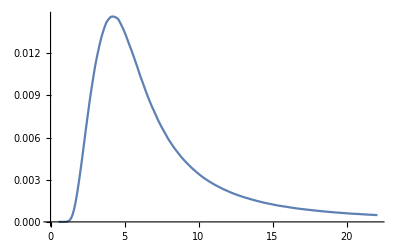

```mathematica
SetDirectory[NotebookDirectory[]];
Clear[tab, tab1];
tab=ReadList["plot5pi.txt",{Number,Number}];
tab1 = {#[[1]],10* Const5π*#[[2]]}&/@tab;
Show[ListPlot[tab1, Joined-> True]]
```

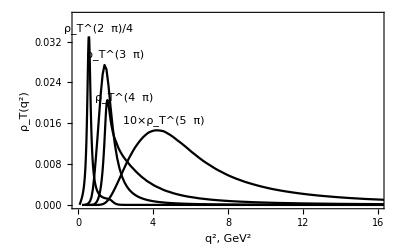

```mathematica
Show[
PlotHST[Fq2π/4,Joined-> True,ShowErrors->False,PlotStyle-> Black, PlotRange->{{0,8},{0,0.033}}],
PlotHST[Fq3π,Joined-> True,ShowErrors->False, PlotRange->{{0,8},{0,0.033}}, PlotStyle-> {Black}],
PlotHST[Fq4πfull,Joined-> True,ShowErrors->False,PlotStyle-> {Black}, PlotRange->{{0,8},{0,0.036}}],
PlotHST[10*$$Fq5π,Joined-> True,ShowErrors->False,PlotStyle-> {Black}, PlotRange->{{0,8},{0,0.036}}],
Frame->True,AxesOrigin->{0,0},FrameLabel->{"q^2, GeV^2","ρ_T(q^2)"},ImageSize->400,PlotRangePadding->0
,Epilog->{Text["ρ_T^(2  π)/4",{1.1,0.0345}],Text["ρ_T^(3  π)",{2,0.0295}],Text["ρ_T^(4  π)",{2.45,0.021}],Text["10×ρ_T^(5  π)",{4.56,0.0165}]},PlotRange->{{0,16},{0,0.037}}
]
Export["spec_funcs.eps",%];
```

### q^2distributions

#### Ξ_cc^(++)→ Λ_c^+

```mathematica
in = "\\Xi_{cc}^{++}";
out = "\\Lambda_{c}^{+}";
Clear[m1, m2, quark1, quark2, f1, f2, g1, g2, Vckm, cS, cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
```

InterpolatingFunction::dmval: Input value TraditionalForm`{0.0779543} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value TraditionalForm`{0.175351} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value TraditionalForm`{0.311707} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

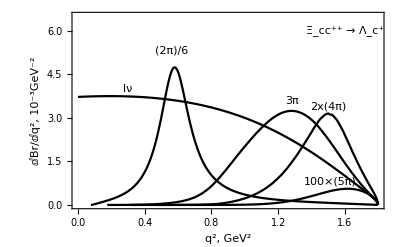

dist1.eps

```mathematica
Show[
Plot[1000*dΓl/fullΓ, {m232, 0,(m1-m2)^2}, PlotStyle->Black], 
Plot[1000*(dΓ2π/fullΓ)/6, {m232, 4mπ^2,(m1-m2)^2}, PlotStyle->Black, PlotRange->All],
 Plot[1000*dΓ3π/fullΓ, {m232, 9mπ^2,(m1-m2)^2}, PlotStyle->Black, PlotRange->All],
 Plot[1000*2*dΓ4πfull/fullΓ, {m232, 16mπ^2,(m1-m2)^2}, PlotStyle->Black, PlotRange->All],
 Plot[1000*100*dΓ5π/fullΓ, {m232, 25mπ^2,(m1-m2)^2}, PlotStyle->Black, PlotRange->All],PlotRange->{All,{0,6.5}},Frame->True,PlotRangePadding->0,FrameLabel->{"q^2, GeV^2" ,"ⅆBr/ⅆq^2, 10^-3GeV^-2"},ImageSize->400,Epilog->{Text["lν",{0.3,4}],Text["(2π)/6",{0.56,5.3}],Text["3π",{1.28,3.57}],Text["2x(4π)",{1.5,3.39}],Text["100×(5π)",{1.51,0.79}],Text[Framed@"Ξ_cc^(++) → Λ_c^+",{1.6,6}]}]
Export["dist1.eps",%]
```

#### Ξ_bc^+ → Ξ_cc^(++)

```mathematica
in = "\\Xi_{bc}^{+}";
out = "\\Xi_{cc}^{++}";
Clear[m1, m2, quark1, quark2, f1, f2, g1, g2, Vckm, cS, cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
```

InterpolatingFunction::dmval: Input value TraditionalForm`{0.0781383} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value TraditionalForm`{0.175535} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value TraditionalForm`{0.311891} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

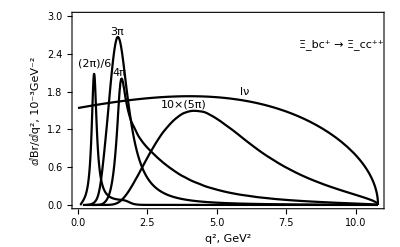

dist2.eps

```mathematica
Show[Plot[1000 dΓl/fullΓ,{m232,0,(m1-m2)^2},PlotStyle->Black],
Plot[1000/6 dΓ2π/fullΓ,{m232,4 mπ^2,(m1-m2)^2},PlotRange->All,PlotStyle->Black],
Plot[1000 dΓ3π/fullΓ,{m232,9 mπ^2,(m1-m2)^2},PlotRange->All,PlotStyle->{Black}],
Plot[1000 dΓ4πfull/fullΓ,{m232,16 mπ^2,(m1-m2)^2},PlotRange->All,PlotStyle->{Black}],
Plot[10*1000 *$$dΓ5π/fullΓ,{m232,25 mπ^2,(m1-m2)^2},PlotRange->All,PlotStyle->{Black}],PlotRange->{All,{0,3}},Frame->True,PlotRangePadding->0,FrameLabel->{"q^2, GeV^2" ,"ⅆBr/ⅆq^2, 10^-3GeV^-2"},ImageSize->400,Epilog->{Text["lν",{6,1.8}],Text["(2π)/6",{0.59,2.24}],Text["3π",{1.39,2.753}],Text["4π",{1.484,2.1}],Text["10×(5π)",{3.8,1.6}],Text[Framed@"Ξ_bc^+ → Ξ_cc^(++)",{9.5,2.55}]}]
Export["dist2.eps",%]
```